```mathematica
SetDirectory[NotebookDirectory[]];
```

## Presné riešenie

{{x$54517→Function[{t},1/2 ⅇ^(-t/2-(√3 t)/2) (1+ⅇ^(√3 t))],y$54517→Function[{t},-1/2 ⅇ^(-t/2-(√3 t)/2) (-1-√3-ⅇ^(√3 t)+√3 ⅇ^(√3 t))]}}

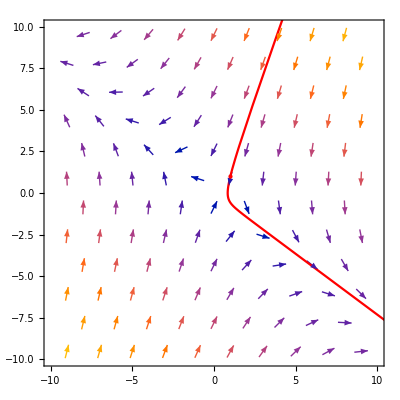

```mathematica
ExactSolution[x0_,y0_,t0_,t1_] := Module[{x, y, M, exactSolution},{
M={{0,-1/2}, {-1,-1}};
exactSolution = DSolve[{
{x'[t],y'[t]}==M.{x[t],y[t]},
x[0]==x0, y[0]==y0},{x,y}, t ];
Print[exactSolution];
{
VectorPlot[M.{x,y},{x, -10,10}, {y,-10,10},VectorPoints->Coarse, VectorSizes->0.5],
ParametricPlot[{{x[t], y[t]}/.exactSolution}, {t,t0,t1}, PlotStyle->Red],
Graphics[{Red,PointSize[Large],Point[{x0,y0}]}]
}
}]
Show[ExactSolution[1,1,-10,10]]
```

```mathematica
Show[ExactSolution[1,1,-10,10]]
```

-Graphics-

## Explicitná Eulerova metóda

### {1, 1}

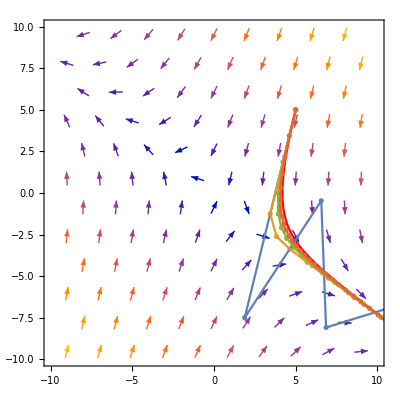

```mathematica
numerics = {Import["./outputs/EEM_1_1_8n.csv","CSV"],
Import["./outputs/EEM_1_1_16n.csv","CSV"],
Import["./outputs/EEM_1_1_32n.csv","CSV"],
Import["./outputs/EEM_1_1_64n.csv","CSV"]};
Show[
ExactSolution[5,5,0,10],
ListPlot[numerics],
ListLinePlot[numerics]
]
```